# Streljanje v ameriških šolah

## Analiza števila smrtnih žrtev in vzvodov za smrtonosne strelske pohode v ameriških šolah

## Pridobivanje podatkov

Za pridobivanje podatkov bom uporabila različne spletne strani, katerih povezave so napisane spodaj. Nekatere podatke bom uredila v Excelu in jih nato vnesla v Mathematico.

```mathematica
Hyperlink["https://en.wikipedia.org/wiki/List_of_school_shootings_in_the_United_States_(before_2000)"]
```

https://en.wikipedia.org/wiki/List_of_school_shootings_in_the_United_States_(before_2000)

```mathematica
Hyperlink["https://en.wikipedia.org/wiki/List_of_school_shootings_in_the_United_States_(2000%E2%80%93present)"]
```

https://en.wikipedia.org/wiki/List_of_school_shootings_in_the_United_States_(2000%E2%80%93present)

```mathematica
Hyperlink["https://en.wikipedia.org/wiki/List_of_school_shootings_in_the_United_States_by_death_toll"]
```

https://en.wikipedia.org/wiki/List_of_school_shootings_in_the_United_States_by_death_toll

```mathematica
Hyperlink["https://worldpopulationreview.com/country-rankings/school-shootings-by-country"]
```

https://worldpopulationreview.com/country-rankings/school-shootings-by-country

```mathematica
Hyperlink["https://www.alfred.edu/about/news/studies/lethal-school-violence/why-do-shootings.cfm"]
```

https://www.alfred.edu/about/news/studies/lethal-school-violence/why-do-shootings.cfm

```mathematica
Hyperlink["https://theconversation.com/5-ways-to-reduce-school-shootings-183965"]
```

https://theconversation.com/5-ways-to-reduce-school-shootings-183965

## Uvod

Streljanja v ameriških šolah predstavljajo perečo problematiko, ki se je v zadnjih desetletjih globoko ukoreninila v ameriški družbi. Pogosti incidenti streljanj povzročajo veliko število smrtnih žrtev in trajne psihične posledice pri preživelih. 
V seminarski nalogi bom analizirala število streljanj in smrtnih žrtev v ameriških šolah in univerzah. Poleg tega bom podatke primerjala z ostalimi državami. Poiskala bom tudi vzroke, ki privedejo do streljanj.

## Strelski pohodi pred letom 2000

## 19. stoletje

*desetletje 1840 == 1840 do 1849

```mathematica
podatki1 = Import["C:\\Users\\Teja\\Desktop\\streljanja v 19. stoletju.xlsx", "Dataset"]
```

{}

```mathematica
Vrednosti11 = Table[podatki1[[1]][[i]][[2]], {i, 2, Length[podatki1[[1]]]}];
```

```mathematica
Vrednosti12 = Table[podatki1[[1]][[i]][[3]], {i, 2, Length[podatki1[[1]]]}];
```

```mathematica
Graf1 = ListLinePlot[Vrednosti11, DataRange->{1840, 1890},PlotStyle -> Purple,  PlotLegends -> {"število streljanj"},AxesLabel->{"Leto"}, Joined->True,AxesOrigin -> {1840, 0}];
```

```mathematica
Graf2 = ListLinePlot[Vrednosti12, DataRange->{1840, 1890},PlotStyle -> Pink, PlotLegends -> {"število smrtnih žrtev"},AxesLabel->{"Leto"}, Joined->True,AxesOrigin -> {1840, 0}];
```

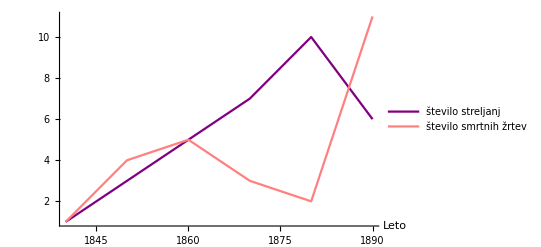

```mathematica
Show[Graf1, Graf2, PlotRange->Automatic]
```

## 20. stoletje

```mathematica
podatki2 = Import["C:\\Users\\Teja\\Desktop\\streljanja v 20. stoletju.xlsx", "Dataset"]
```

{}

```mathematica
Vrednosti21 = Table[podatki2[[1]][[i]][[2]], {i, 2, Length[podatki2[[1]]]}];
```

```mathematica
Vrednosti22 = Table[podatki2[[1]][[i]][[3]], {i, 2, Length[podatki2[[1]]]}];
```

```mathematica
Graf1 = ListLinePlot[Vrednosti21, DataRange->{1900, 1990},PlotStyle -> Purple,  PlotLegends -> {"število streljanj"},AxesLabel->{"Leto"}, Joined->True,AxesOrigin -> {1900, 0}];
```

```mathematica
Graf2 = ListLinePlot[Vrednosti22, DataRange->{1900, 1990},PlotStyle -> Pink, PlotLegends -> {"število smrtnih žrtev"},AxesLabel->{"Leto"}, Joined->True,AxesOrigin -> {1900, 0}];
```

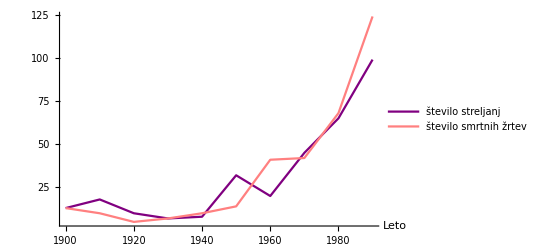

```mathematica
Show[Graf1, Graf2, PlotRange->Automatic]
```

## Strelski pohodi po letu 2000

## 21. stoletje

```mathematica
podatki3 = Import["C:\\Users\\Teja\\Desktop\\streljanja v 21. stoletju.xlsx", "Dataset"]
```

{}

```mathematica
Vrednosti31 = Table[podatki3[[1]][[i]][[2]], {i, 2, Length[podatki3[[1]]]}];
```

```mathematica
Vrednosti32 = Table[podatki3[[1]][[i]][[3]], {i, 2, Length[podatki3[[1]]]}];
```

```mathematica
Graf1 = ListLinePlot[Vrednosti31, DataRange->{2000, 2020},PlotStyle -> Purple,  PlotLegends -> {"število streljanj"},AxesLabel->{"Leto"}, Joined->True,AxesOrigin -> {2000, 0}];
```

```mathematica
Graf2 = ListLinePlot[Vrednosti32, DataRange->{2000, 2020},PlotStyle -> Pink, PlotLegends -> {"število smrtnih žrtev"},AxesLabel->{"Leto"}, Joined->True,AxesOrigin -> {2000, 0}];
```

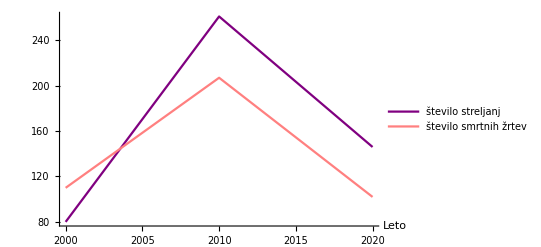

```mathematica
Show[Graf1, Graf2,PlotRange->Automatic]
```

## Strelski pohodi v letu 2023

```mathematica
podatki4 = Import["C:\\Users\\Teja\\Desktop\\streljanja 2023.xlsx", "Dataset"]
```

{}

```mathematica
Vrednosti41 = Table[podatki4[[1]][[i]][[2]],{i,2,Length[podatki4[[1]]]}];
```

```mathematica
Vrednosti42 = Table[podatki4[[1]][[i]][[3]],{i,2,Length[podatki4[[1]]]}];
```

```mathematica
Graf1 = ListLinePlot[Vrednosti41, DataRange->{1, 8},PlotStyle -> Purple,  PlotLegends -> {"število streljanj"},AxesLabel->{"Mesec"}, Joined->True,AxesOrigin -> {1, 0}];
```

```mathematica
Graf2 = ListLinePlot[Vrednosti42, DataRange->{1, 8},PlotStyle -> Pink,  PlotLegends -> {"število smrtnih žrtev"},AxesLabel->{"Mesec"}, Joined->True,AxesOrigin -> {1, 0}];
```

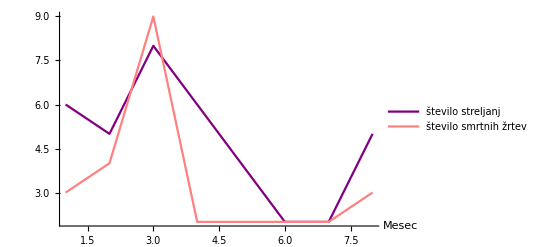

```mathematica
Show[Graf1, Graf2, PlotRange->Automatic]
```

## Strelski pohodi od 1840 do 2020

```mathematica
podatki5 = Import["C:\\Users\\Teja\\Desktop\\streljanja.xlsx", "Dataset"]
```

{}

```mathematica
Vrednosti51 = Table[podatki5[[1]][[i]][[2]],{i,2,Length[podatki5[[1]]]}];
```

```mathematica
Vrednosti52 = Table[podatki5[[1]][[i]][[3]],{i,2,Length[podatki5[[1]]]}];
```

```mathematica
Graf1 = ListLinePlot[Vrednosti51, DataRange->{1840, 2020},PlotStyle -> Purple,  PlotLegends -> {"število streljanj"},AxesLabel->{"Leto"}, Joined->True,AxesOrigin -> {1840, 0}];
```

```mathematica
Graf2 = ListLinePlot[Vrednosti52, DataRange->{1840,2020},PlotStyle -> Pink, PlotLegends -> {"število smrtnih žrtev"},AxesLabel->{"Leto"}, Joined->True,AxesOrigin -> {1840, 0}];
```

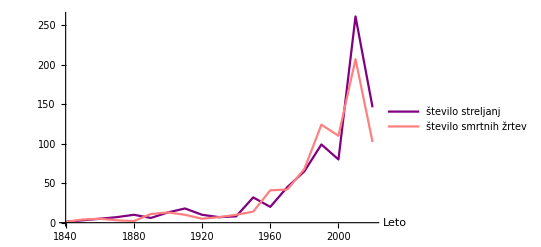

```mathematica
Show[Graf1, Graf2, PlotRange->Automatic]
```

Vidimo, da sta tako število streljanj kot število smrtnih žrtev iz desetletja v desetletje do leta 1950 počasi naraščali, od leta 2000 pa se številke drastično povečujejo.

## 10 najsmrtonosnejših strelskih pohodov v zgodovini ZDA

```mathematica
podatki6 = Import["C:\\Users\\Teja\\Desktop\\10 najsmrtonosnejsih.xlsx", "Dataset"]
```

{}

## Primerjava z ostalimi državami

Spodnja tabela prikazuje države z najvišjim številom strelskih incidentov v šolah od januarja 2009 do maja 2018.

```mathematica
podatki7 = Import["C:\\Users\\Teja\\Desktop\\streljanja po drzavah.xlsx", "Dataset"]
```

{}

```mathematica
drzave = Table[podatki7[[1]][[i]][[1]], {i, 2, Length[podatki7[[1]]]}];
```

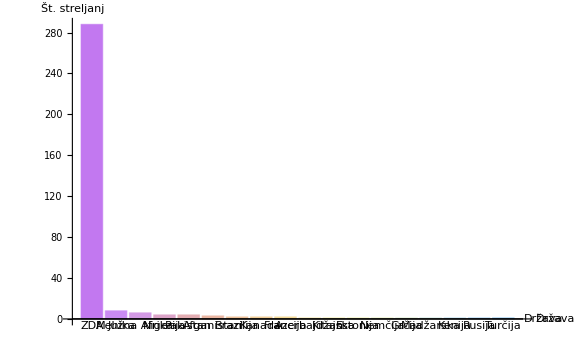

```mathematica
BarChart[{288,8,6,4,4,3,2,2,2,1,1,1,1,1,1,1,1,1}, ChartLabels->{drzave}, ImageSize->Large, AxesLabel->{"Država","Št. streljanj"},ChartStyle->"Pastel"]
```

Iz diagrama je razvidno, da streljanje v šolah predstavlja tako velik problem le Združenim državam Amerike, saj so v skoraj 10 letih našteli kar 288 strelskih napadov. Daleč zadaj, na 2. mestu, je Mehika, z 8 napadi.

## Vzroki

```mathematica
podatki8 = Import["C:\\Users\\Teja\\Desktop\\Vzroki.xlsx", "Dataset"]
```

{}

```mathematica
PieChart[{11.1,11,7.9,7.8,7.2,7.2,7,6.9,6.7,6.3,4.7,4.4,3.6,3.3,2.6,2.3},ChartLegends->{"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16"},ChartStyle->"Pastel"]
```

-Graphics-

Največji vzrok za strelske napade je psihično in fizično nadlegovanje ter zbadanje s strani vrstnikov. S tem problemom se soočajo (večinoma) vse države, vendar je v ZDA orožje dostopnejše in zato tudi večkrat pride do tovrstnih napadov.

## Rešitev

```mathematica
uvod = "After the school shooting in Parkland,Florida,in 2018,psychology professor Paul Boxer and his colleagues reviewed research to see what could be learned from what they refer to as the “science of violence prevention.” In the wake of the May 24,2022,massacre at Robb Elementary School in Uvalde,Texas,Boxer has revisited that research anew–and other research conducted since then–for insights on what can be done to reduce the risk of school shootings in the future.Here he offers five policy changes–based on his findings–that can be implemented to achieve that end.";
```

```mathematica
TextTranslation[uvod, #]&/@{"Slovenian"}
```

{Po streljanju v šoli v Parklandu na Floridi leta 2018 so profesor psihologije Paul Boxer in njegovi kolegi pregledali raziskave, da bi ugotovili, kaj bi se lahko naučili iz tega, kar imenujejo "znanost o preprečevanju nasilja". Po pokolu 24. maja 2022 na osnovni šoli Robb v Uvaldeju v Teksasu je Boxer ponovno preučil to raziskavo - in druge raziskave, izvedene od takrat - za vpogled v to, kaj je mogoče storiti za zmanjšanje tveganja streljanja v šoli v prihodnosti. Tukaj ponuja pet sprememb politike - na podlagi njegovih ugotovitev - ki jih je mogoče izvesti za dosego tega cilja.}

Spremembe, navedene v njihovem članku:
1. Drastična omejitev dostopa do strelnega orožja.
2. Večja uporaba ocenjevanj tveganja za nasilje v šolah.
3. Razširitev strategij, ki temeljijo na dokazih, za zmanjšanje nasilnega vedenja.
4. Varnejše šolske zgradbe.
5. Zmanjšanje izpostavljenosti nasilju na družbenih omrežjih in v medijih.